IPPT Model (Argon)

2d. Multiple-Pulse Solver for Ambient Backpressure

	Instructions:
	- This notebook will evaluate the single-pulse model multiple times using a single set of initial conditions
	- This notebook differs from 2b by implementing an ambient backpressure that modifies the baseline neutral background distribution in the inter-pulse regime
	
	How to Run:
	- Define the input conditions you desire under “Inputs”
	- Click “Evaluate Notebook” in Menu Options
	- Key performance metrics and steady-state and neutral diffusion will output for each pulse, use “3. Single Case Plots” to visualize model results

Physical Constants

```mathematica
kb=1.38 10^-23;   
ec=1.6 10^-19;    
me=9.11 10^-31; 
AW=40; 
mi=AW 1.67 10^-27;      
un=((kb 298)/mi)^(1/2);
Tn=298/11604.5; (* Ambient Gas Temperature (eV) *)
σqm = 1.57 10^-18; (* Ar-Ar+ momentum transfer cross section, Phelps 1991 *)
```

Multi-Pulse Solver Function

```mathematica
MPSolve[zmax_,zsteps_,tmax_,tsteps_,zs0_,ws0_,nn0_,χi0_,zχi_,Te0_,Ti0_,zn_,Lc_,L0_,Rc_,C0_,V0_,zc_,zc0_,rout_,rin_,nn0z_,frep_,Np_,Ptest_]:=Module[{},
Trep =1/frep; (* Pulse repition period *)
nn0zt[z_]=nn0z[z]; (* Initialize nn0 function *)

(** Output data placeholders **)
nn0table=Table[Null,{j,1,Np}];  (* Pre-pulse neutral distribution *)
Isptable=Table[Null,{j,1,Np}];  (* Specific impulse *)
nttable=Table[Null,{j,1,Np}];  (* Thruster efficiency w/o energy recovery *)
ntrectable=Table[Null,{j,1,Np}];  (* Thruster efficiency w/ energy recovery *)
nmtable=Table[Null,{j,1,Np}];  (* Mass utilization efficiency *)
piion1table=Table[Null,{j,1,Np}];  (* Πion first form *)
piion2table=Table[Null,{j,1,Np}];  (* Πion second form *)
picextable=Table[Null,{j,1,Np}];  (* Πcex *)

tval = AbsoluteTime[];
p = 1; (* Initialize pulse = 1 *)
While[p≤ Np,
Print["p = ", p]; (* Pulse # *)
nn0table[[p]]=nn0zt[z]; (* Pre-pulse neutral distribution *)

(** IPPT single-pulse model **)
SPSolve[zmax,zsteps,tmax,tsteps,zs0,ws0,nn0,χi0,zχi,Te0,Ti0,zn,Lc,L0,Rc,C0,V0,zc,zc0,rout,rin,nn0zt];

(** Inter-pulse neutral distribution update **)
nn0ap[z_]=nnout[z,tmaxt]; (* nn0 after pulse p *)
Dn=Min[Sqrt[π]/(nsout[tmax]σcx+nfout[tmax]σqm)un,1];    (* Neutral diff coeff - Kelly 2020 *)
solp= NDSolve[{
Derivative[0,1][nn][z,t]== -un*Derivative[1,0][nn][z,t]+Dn Derivative[2,0][nn][z,t]-(nn[z,t]-(133.3 Ptest)/(ec Tn))/(rout/un)UnitStep[((133.3 Ptest)/(ec Tn)-nn[z,t])], (* Continuity eqn *)
nn[z,0]==nn0ap[z],
nn[0,t]==(nn0-nn0ap[0]) (t/(10^-8+t)) +nn0ap[0] 
},nn,{z,0,1.2 zmax},{t,0,Trep}];
nnfpp=nn/.solp[[1]]; 
nn0pp[z_]=nnfpp[z,Trep];

(** Redefine pre-pulse neutral distribution **)
nn0zt[z_]=nn0pp[z];      (* Numerical PDE solver result *)

(** Update performance metric tables post-pulse **)
Isptable[[p]]=Isp[tmaxt];
nttable[[p]]=ηT[tmaxt];
ntrectable[[p]]=ηTrec[tmaxt];
nmtable[[p]]=ηm[tmaxt];
piion1table[[p]]=Πiont[tmaxt];
piion2table[[p]]=Πiont2[tmaxt];
picextable[[p]]=Πcext2[tmaxt];

(** Store first-pulse data **)
If[p==1,
nnii=nnout;
wsii=wsout;
zsii=zsout;
vsii=vsout;
vfii=vfout;
nsii=nsout;
nfii=nfout;
Icii=Icout;
Ipii=Ipout;
Mii=Mout;
Vii=Vout;
Teii=Teout;
Tiii=Tiout;
psii=psout;
KEsii=KEsout;
Efii=Efout;
mbitii=mbit;
msii[t]=ms[t];
Epiii=Epi;
Eelii=Eel;
Eindii[t]=Eind[t];
Ecapii[t]=Ecap[t];
Ekeii[t]=Eke[t];
EkePlii[t]=EkePl[t];
EkeEntii[t]=EkeEnt[t];
Eteii[t]=Ete[t];
Ibitii[t]=Ibit[t];
Ispii[t]=Isp[t];
ηmii[t]=ηm[t];
MassFracii[t]=MassFrac[t];
ηTii[t]=ηT[t];
ηTrecii[t]=ηTrec[t];
Πiontii[t]=Πiont[t];
Πiont2ii[t]=Πiont2[t];
Πcext2ii[t]=Πcext2[t];
];

(** Store final-pulse data **)
If[p==Np,
nnff=nnout;
wsff=wsout;
zsff=zsout;
vsff=vsout;
vfff=vfout;
nsff=nsout;
nfff=nfout;
Icff=Icout;
Ipff=Ipout;
Mff=Mout;
Vff=Vout;
Teff=Teout;
Tiff=Tiout;
psff=psout;
KEsff=KEsout;
Efff=Efout;
mbitff=mbit;
msff[t]=ms[t];
Epiff=Epi;
Eelff=Eel;
Eindff[t]=Eind[t];
Ecapff[t]=Ecap[t];
Ekeff[t]=Eke[t];
EkePlff[t]=EkePl[t];
EkeEntff[t]=EkeEnt[t];
Eteff[t]=Ete[t];
Ibitff[t]=Ibit[t];
Ispff[t]=Isp[t];
ηmff[t]=ηm[t];
MassFracff[t]=MassFrac[t];
ηTff[t]=ηT[t];
ηTrecff[t]=ηTrec[t];
Πiontff[t]=Πiont[t];
Πiont2ff[t]=Πiont2[t];
Πcext2ff[t]=Πcext2[t];
];

(** Print results for each pulse **)
Print["t = ",(AbsoluteTime[]-tval)/60," minutes"];
Print["Isp = ",Isp[tmaxt]," seconds"];
Print["Thruster Efficiency w/o Energy Recovery = ", ηT[tmaxt]];
Print["Thruster Efficiency w/ Energy Recovery = ",ηTrec[tmaxt]];
Print["Mass Utilization Efficiency = ",ηm[tmaxt]];
Print["Plasma Density in the Current Sheet = ", nsout[tmaxt]];

Print[
LogPlot[nn0table,{z,0,zmax},PlotRange->All,Frame->True,
ImageSize->400,
PlotLabel->"Neutral Density at Each Pulse",
FrameLabel->{"Distance, z (m)","Neutral Density  (m^-3)"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle-> {FontFamily->"Times"}]
];
Print[
LogPlot[{nn0ap[z],nn0pp[z]},{z,0,zmax},PlotRange->All,Frame->True,
ImageSize->400,
PlotLabel->"Interpulse Neutral Density Conversion",
FrameLabel->{"Distance, z (m)","Neutral Density  (m^-3)"},
PlotLegends-> {"Aft pulse p","Pre pulse p+1"},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle-> {FontFamily->"Times"}]
];
If[Np>1,
Print[PulsePlot[Isptable,"Specific Impulse","I_sp (s)"]];
Print[PulsePlot[ntrectable,"Thruster Efficiency","η_T"]];
Print[PulsePlot[nmtable,"Mass Utilization Efficiency","η_m"]];];
Print[TimePlot[Isp,"Specific Impulse","I_sp (s)",tmax]];
Print[EffTimePlot[ηTrec,"Thruster Efficiency","η_T",tmax]];
Print[EffTimePlot[ηm,"Mass Utilization Efficiency","η_m",tmax]];
p++]]
```

Inputs

```mathematica
(** From Single Case Solver **)
zmaxt=0.2;        (* Axial boundary of simulation *)
zstepst=500;       (* Number of axial gridpoints *)
tmaxt=6.28 10^-6;    (* Maximum time of simulation *)
tstepst=500;      (* Number of timesteps *)
zs0t=0.0;          (* Initial current sheet location *)
ws0t=0.002;       (* Initial current sheet width, or width of pre-ionized plasma *) 
χi0t=0.01;       (* Pre-ionization fraction *)
zχit=ws0t;        (* Pre-ionization length scale *)
nn0t=9.7 10^19;    (* Characteristic ambient neutral density *)
znt=0.01;     (* Characteristic ambient neutral length scale *)
Te0t=20;       (* Initial electron temperature *)
Ti0t=0.1;     (* Initial ion temperature *) 
Lct=500 10^-9;   (* Coil inductance *)
L0t=50 10^-9;   (* Stray inductance *)
Rct=0.005;   (* Coil resistance *)
C0t=2 10^-6;   (* Capacitance *)
V0t=3000;    (* Capacitor voltage *)
zct=0.04;   (* Coil mutual coupling distance *)
zc0t = -0.002; (* Location of coil wrt neutral gas injection plane *)
rtout= 0.1;   (* Thruster outer radius *)
rtin = 0.03; (* Thruster inner radius *)
nn0z[z_]=nn0t Exp[-z/znt]; (* Ambient neutral density distribution prior to PI *)

(** Unique to Multi-Pulse Solver **)
frept = 10000; (* Pulse repitition rate [Hz] *)
Npt = 6; (* Number of pulses *)

(** Unique to Backflow Solver **)
Ptestt = 1 10^-3; (* Test pressure [Torr] *)
```

Solver and Data Visualization

p = 1

InterpolatingFunction::dmval: Input value {0.205,6.28×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.21,6.28×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.215,6.28×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable z.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable z. Artificial boundary effects may be present in the solution.

t = 1.81293514 minutes

Isp = 2784.72 seconds

Thruster Efficiency w/o Energy Recovery = 0.0767962

Thruster Efficiency w/ Energy Recovery = 0.305086

Mass Utilization Efficiency = 0.265828

Plasma Density in the Current Sheet = 1.49653×10^19

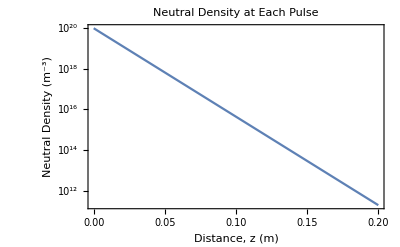

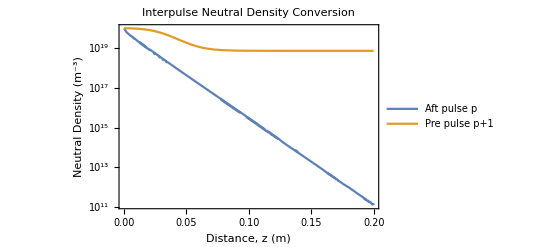

-Graphics-

-Graphics-

-Graphics-

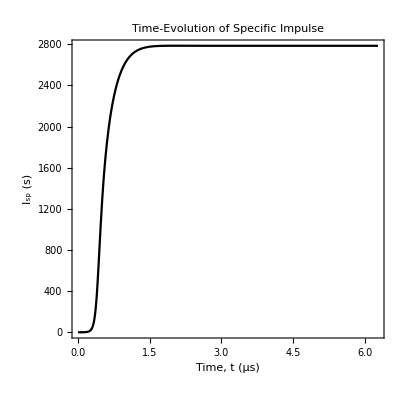

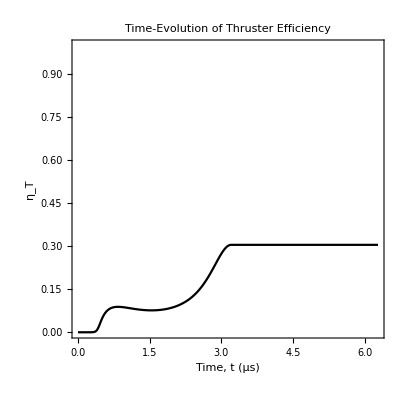

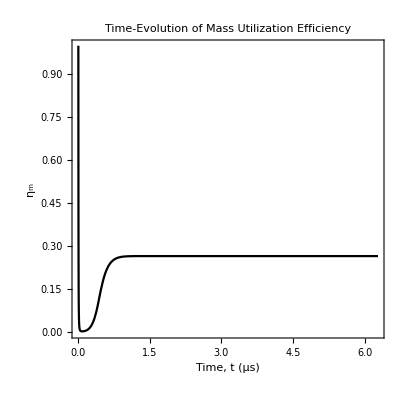

p = 2

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable z.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable z. Artificial boundary effects may be present in the solution.

t = 4.39046819 minutes

Isp = 960.79 seconds

Thruster Efficiency w/o Energy Recovery = 0.0411534

Thruster Efficiency w/ Energy Recovery = 0.142657

Mass Utilization Efficiency = 0.510721

Plasma Density in the Current Sheet = 6.50148×10^20

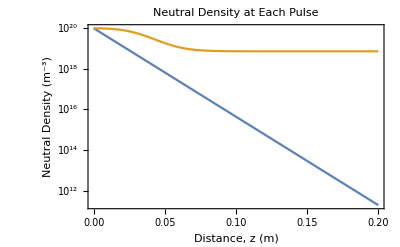

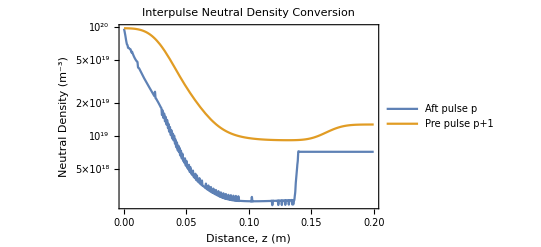

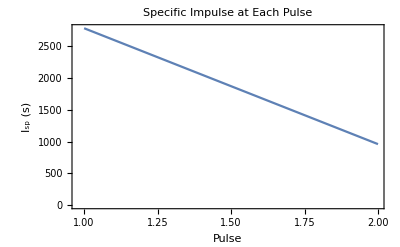

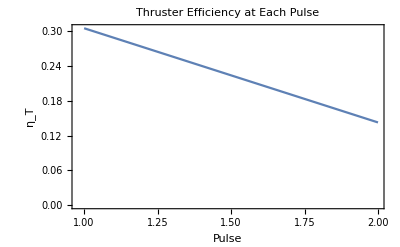

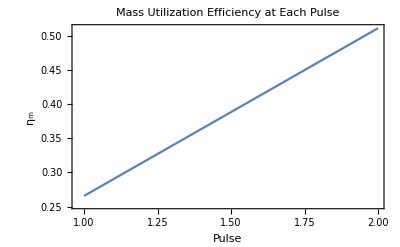

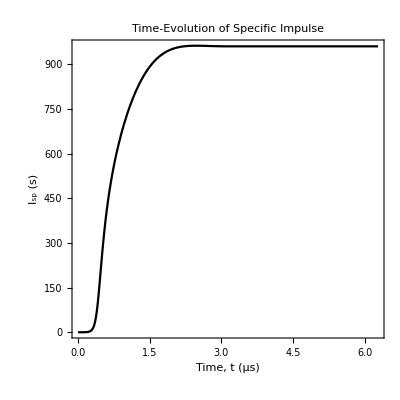

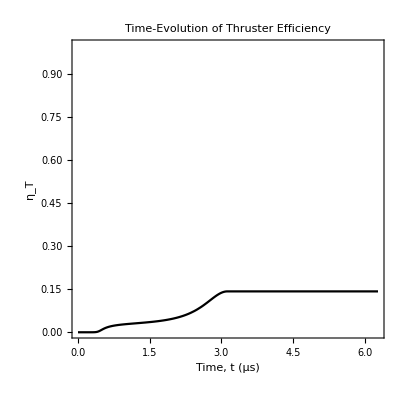

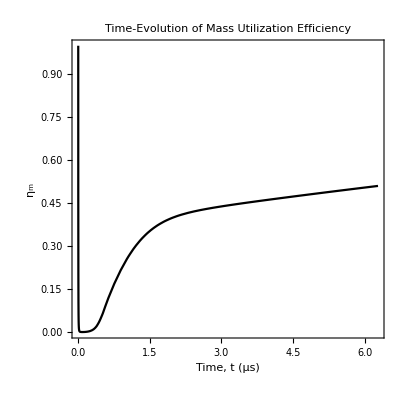

p = 3

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable z.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable z. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.

t = 6.950950795 minutes

Isp = 778.226 seconds

Thruster Efficiency w/o Energy Recovery = 0.0328609

Thruster Efficiency w/ Energy Recovery = 0.114052

Mass Utilization Efficiency = 0.488478

Plasma Density in the Current Sheet = 6.75525×10^20

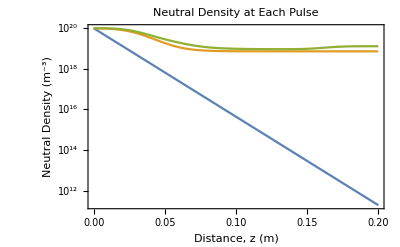

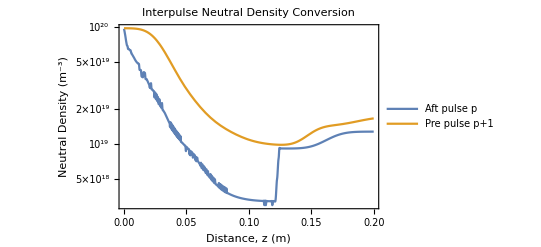

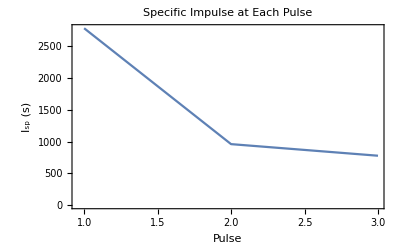

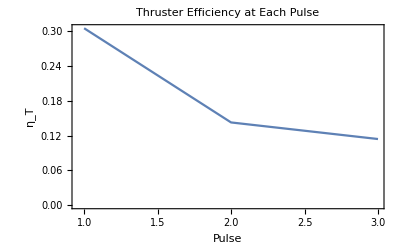

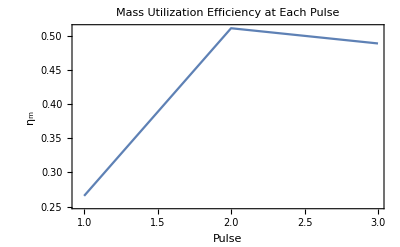

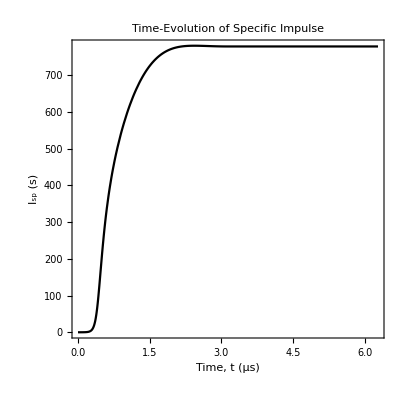

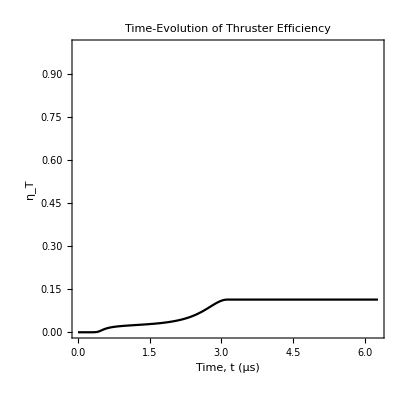

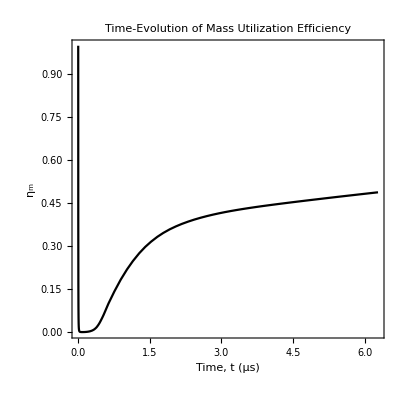

p = 4

t = 9.566005575 minutes

Isp = 727.457 seconds

Thruster Efficiency w/o Energy Recovery = 0.0306616

Thruster Efficiency w/ Energy Recovery = 0.106499

Mass Utilization Efficiency = 0.474434

Plasma Density in the Current Sheet = 6.7803×10^20

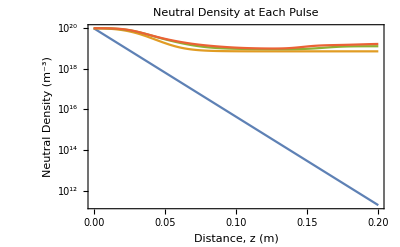

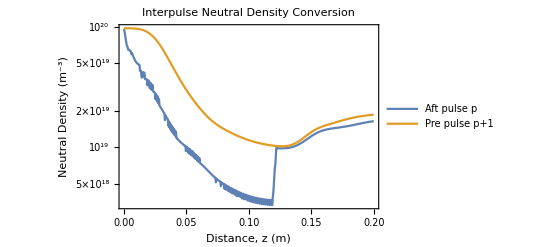

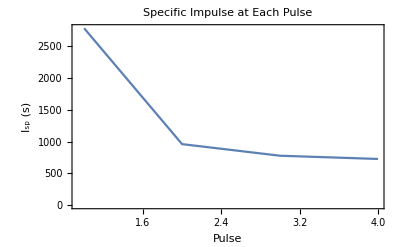

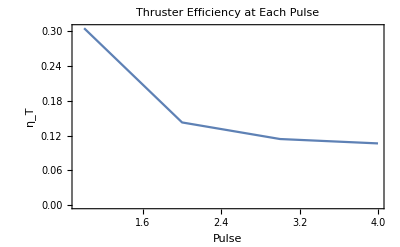

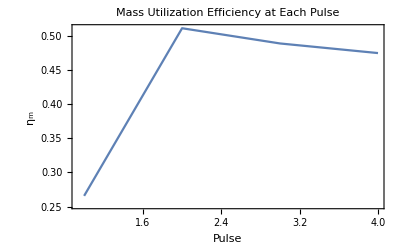

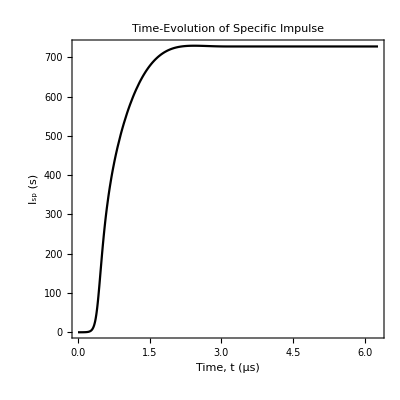

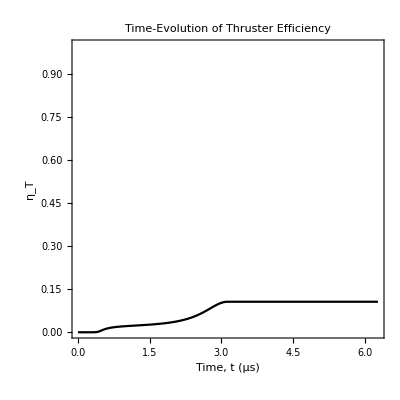

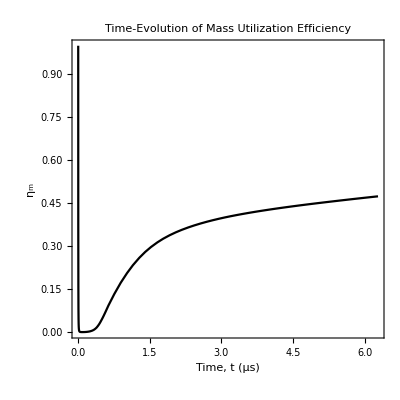

p = 5

t = 12.29664738 minutes

Isp = 707.445 seconds

Thruster Efficiency w/o Energy Recovery = 0.0297848

Thruster Efficiency w/ Energy Recovery = 0.103479

Mass Utilization Efficiency = 0.466411

Plasma Density in the Current Sheet = 6.78292×10^20

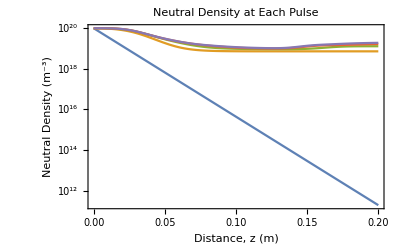

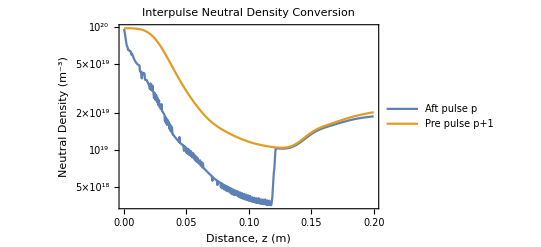

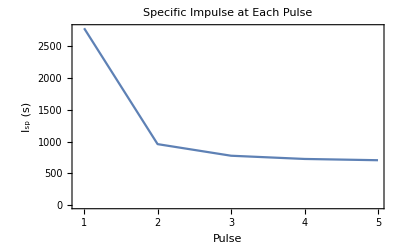

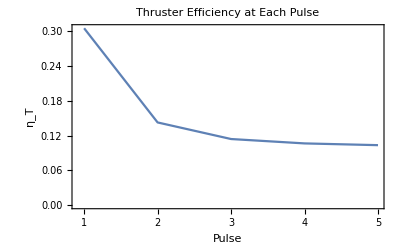

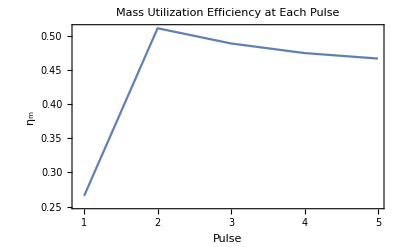

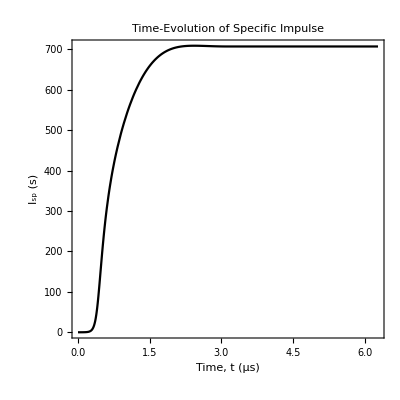

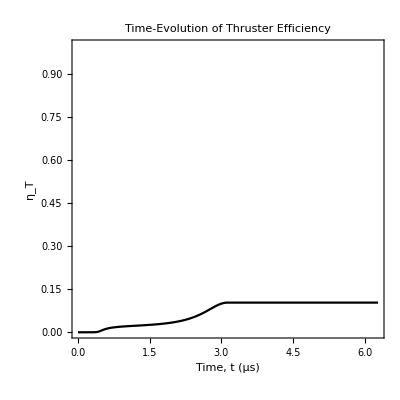

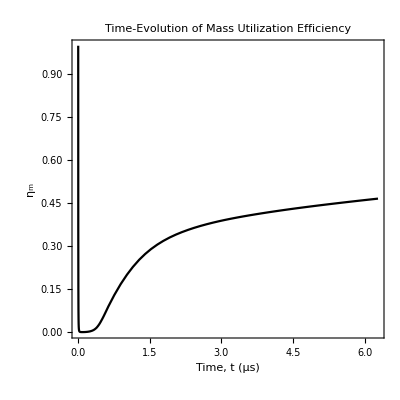

p = 6

t = 15.15110767 minutes

Isp = 700.274 seconds

Thruster Efficiency w/o Energy Recovery = 0.0294811

Thruster Efficiency w/ Energy Recovery = 0.102424

Mass Utilization Efficiency = 0.463502

Plasma Density in the Current Sheet = 6.7912×10^20

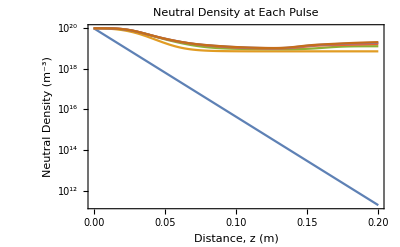

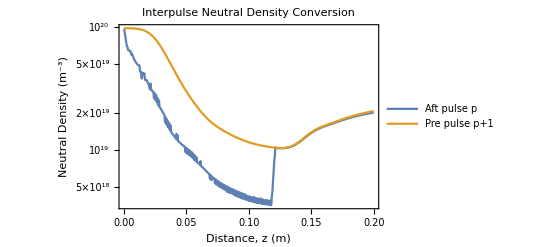

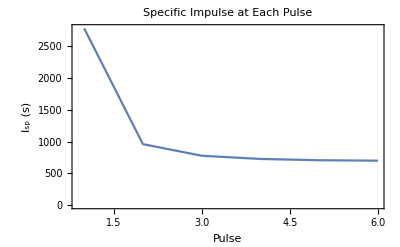

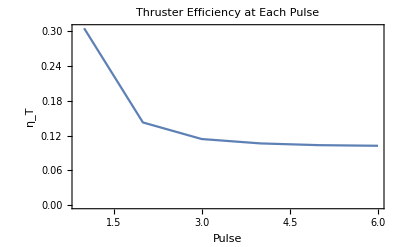

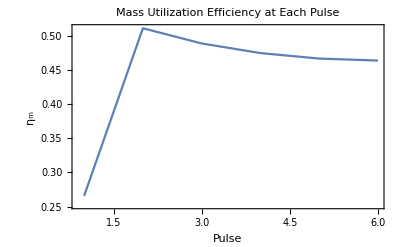

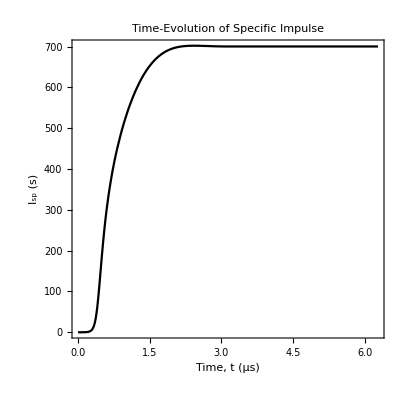

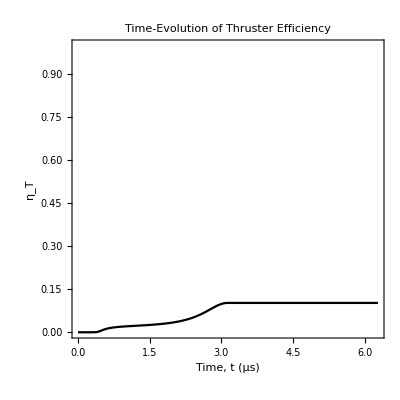

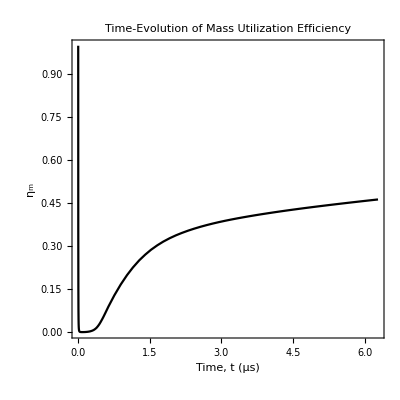

```mathematica
(* Fix possible overwrite *)
nn0zt[z_]=nn0z[z];

MPSolve[zmaxt,zstepst,tmaxt,tstepst,zs0t,ws0t,nn0t,χi0t,zχit,Te0t,Ti0t,znt,Lct,L0t,Rct,C0t,V0t,zct,zc0t,rtout,rtin,nn0zt,frept,Npt,Ptestt];
```